{$CellContext`datafilename1OpenAll,}

C:\A\Notes\PRG\W\WolfThermography\3\DfIR553s4_1.dat File exists

{312,232}

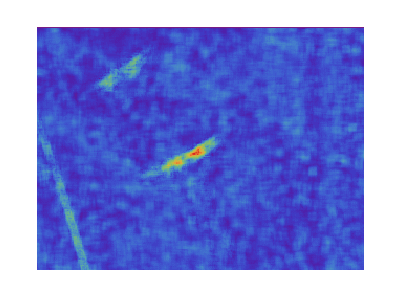

```mathematica
ClearAll["Global'*"];
Needs["PlotLegends`"](* PlotLegends is now obsolete*) 
Evaluate[{FileNameSetter[Dynamic[datafilename1]],Dynamic[datafilename1]}] 
If[FileExistsQ[datafilename1],Print["File exists "datafilename1],Print["This File does not exist"];Quit[]];
 data1=Import[datafilename1];
memoryTem=0;
mtxw=320; mtxh=240; sw=4; sh=3; 
redw=Round[mtxw/sw]; redh=Round[mtxh/sh];
Temperaturethreshold=.3;  showmesh=False;TechError=0.05;
FilterForErrorMagnitude1=1;

colorsGoody={RGBColor[0.05374,0,0.333],RGBColor[0.0979,0,0.467],RGBColor[0,0,1],RGBColor[0.2,1,0.96],RGBColor[0,0.93,0.07519],RGBColor[1,1,0],RGBColor[1,0,0],Darker[RGBColor[1,0,0],.4]};
Dimensions[data1]
data1=Transpose[data1];
For[i=1,i≤ Dimensions[data1][[1]],i++,{
For[j=1,j≤ Dimensions[data1][[2]],j++,{
data1[[i,j]]-=2;
If[i<2,data1[[i,j]]=0;]; 

}]
}]
ArrayPlot[data1,PlotRange->All,ColorFunction->"Rainbow",Mesh->showmesh,ClippingStyle->Automatic,PlotLegends->Placed[Automatic,Below],ColorFunctionScaling->True] 
(*Histogram[Flatten[data1],Automatic,"PDF"]*)
Drop[data1,2];
data1=Flatten@data1;
Manipulate[Show[{Histogram[Select[Select[Sort[data1,#2>#1 &],#>left&],#<right&],{bin},Automatic](*,SmoothHistogram[Select[Select[Sort[data1,#2>#1 &],#>left&],#<right&]]*)}],{bin,0.000001,0.01,0.000001},{right,Max[data1],Min[data1],(Max[data1]-Min[data1])/10000},{left,Min[data1],Max[data1],-(Max[data1]-Min[data1])/10000}]
```

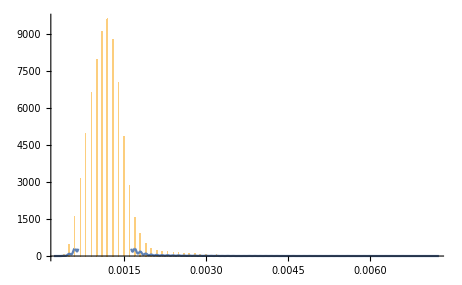
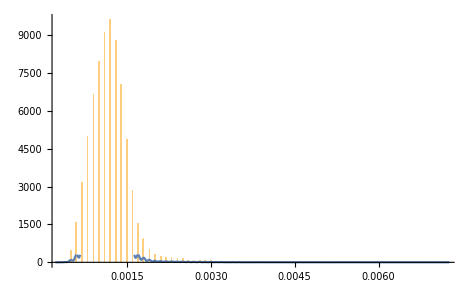
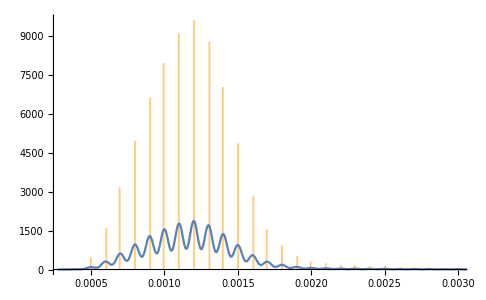
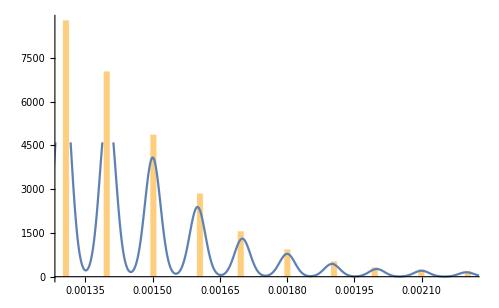
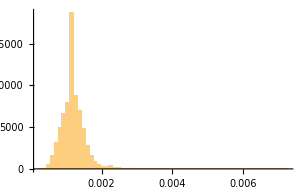
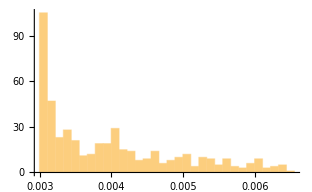

```mathematica
Manipulate[ImageHistogram[-Graphics-,n,{left,right},Method->clip,Joined->join,Appearance->m],{{n,128},1,256,1},{{left,0},-1,1.5},{{right,1},-0.5,1.5},{clip,{"IncludeOutOfRange","ExcludeOutOfRange"}},{join,{True,False}},{{m,"RGB","Appearance"},{"Transparent","RGB","Stacked","Separated"}}]
```

```mathematica
Manipulate[ImageHistogram[-Graphics-,n,{left,right}],{{n,128},1,256,1},{{left,0},-1,1.5},{{right,1},-0.5,1.5}]
```

```mathematica
a={1,1,1,2,2,5,5,7,7,8,8,8,8,8,9,0,1,11,12,12,15,12,1};
Dimensions[a][[1]]
(*Manipulate[Histogram[a,{st}],{st,.1,2,.1}]*)
Manipulate[Histogram[Sort[a,#2>#1 &], {bin}],{bin,.1,3,.1}]
```

23

```mathematica
a={1,1,1,2,2,5,5,7,7,8,8,8,8,8,9,0,1,11,12,12,15,12,1};
Manipulate[Histogram[Select[Select[Sort[a,#2>#1 &],#>left &],#<right &], {bin}],{bin,.1,3,.1},{right,Max[a],Min[a],-0.1},{left,Min[a],Max[a],0.1}]
```

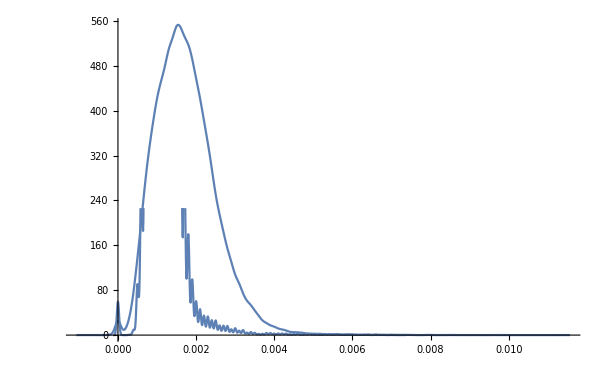

```mathematica
d53s3:={{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,74533,0.0020999999999999908,0.0019999999999997797,0.0024000000000001798,0.0017000000000000348,0.001100000000000101,0.001100000000000101,0.000700000000000145,0.0005999999999999339,0.0011999999999998678,0.0011999999999998678,0.0013000000000000789,0.001100000000000101,0.0015000000000000568,0.0017000000000000348,0.0013999999999998458,0.0015000000000000568,0.0013000000000000789,0.0015999999999998238,0.0020999999999999908,0.0019000000000000128,0.0015999999999998238}}, {{{, , , , }}}};
d53s4:={{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,72341,0.0015000000000000568,0.0013000000000000789,0.0013000000000000789,0.0013000000000000789,0.0013000000000000789,0.0011999999999998678,0.001100000000000101,0.001100000000000101,0.001100000000000101,0.0013000000000000789,0.0013000000000000789,0.0013000000000000789,0.0013000000000000789,0.0015000000000000568,0.0013000000000000789,0.0011999999999998678,0.0011999999999998678,0.0011999999999998678,0.001100000000000101,0.001100000000000101,0.001100000000000101}}, {{{, , , , }}}};
Show[{SmoothHistogram[d53s3],SmoothHistogram[d53s4]}]
```